# Test NNTracePlot

These tests require the standard test file resources folder to be downloaded from Git and available at Tests/_resources.

## Initialization

```mathematica
<<NounouW`
```

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

HokahokaW`
Tue 8 Nov 2016 00:49:32     [Mathematica: 11.0.1 for Microsoft Windows (64-bit) (September 20, 2016)]
     Artifact info as of: Sun 14 Aug 2016 00:05:06
     Local repo path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [e54e12e7076ab93c52f9fd04b9ad2cd5bd18b862]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

<<Set JLink` java stack size to 6144Mb>>

NounouW`
Tue 8 Nov 2016 00:49:32     [Mathematica: 11.0.1 for Microsoft Windows (64-bit) (September 20, 2016)]
     Artifact info as of: Sun 23 Oct 2016 15:55:26
     Local repo path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  master [7741dc2ed66a16c85ad319d82d87c9c89810f87d]
     Remote:  origin (https://github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

Welcome to nounou, a Scala/Java adapter for neurophysiological data.\nLast GIT info from file resource: NNGit.gson.txt\n  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e\n  + current branch is: master\n  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git\n

```mathematica
Get[ FileNameJoin[{Nest[ParentDirectory,SetDirectory[NotebookDirectory[]],1],"TestDataLoaders.m"}] ];
$nnwResourcesFolder
```

C:\prog\_w\NounouW\resources

```mathematica
(*ShowJavaConsole[]*)
```

## BG006

```mathematica
NNWTestLoadBG006
```

$nnwTestFileFolder = C:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12

$nnwTestFiles = C:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC13.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC14.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC15.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC16.ncs

```mathematica
NNPrintInfo[$nnwTestDataOri, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	  19244544 ( 10:01.39) (   601.4)	   261898230 ( 0:00.00)

### NNTracePlot

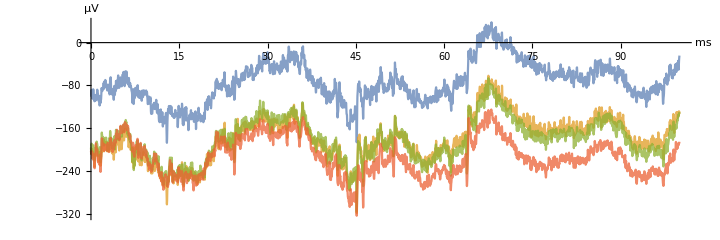

```mathematica
NNTracePlot[$nnwTestDataOri, All, {0 ;; 3200, 0}, NNOptAmplificationFactor-> 16]
```

done

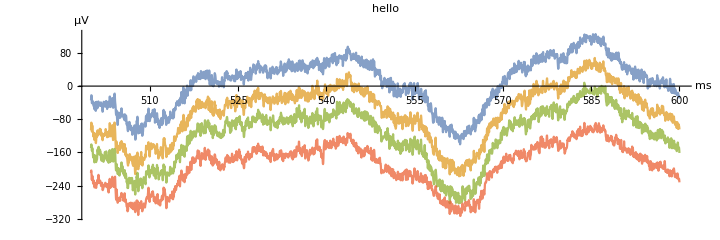

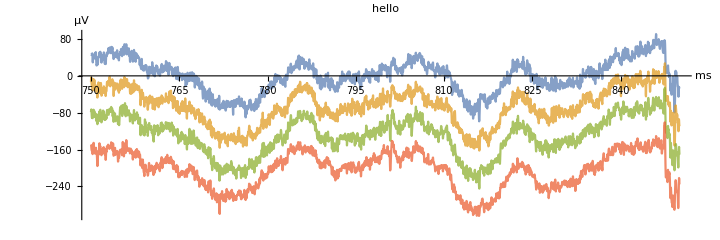

```mathematica
NNTracePlotManipulate[$nnwTestDataOri, All, Automatic, NNOptAmplificationFactor-> 16]
```

```mathematica
$nnwTestDataMedianSubtract=NNFilterMedianSubtract[$nnwTestDataOri, 81]
```

```mathematica
$nnwTestDataOri@timing[]@segmentLength[0]
```

19244544

## SPP067a

```mathematica
NNWTestLoadSPP067a
```

$nnwTestFileFolder = C:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a

$nnwTestFiles = C:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC5.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC6.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC7.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\SPP067\a\CSC8.ncs

```mathematica
$nnwTestDataOri
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
$nnwTestDataOri@channelCount[]
```

4

### Timing information

```mathematica
NNPrintInfo[$nnwTestDataOri]
```

nounou.elements.data.NNDataChannelArray(1 segments, fs=32000.0,  , 1a58c41332)
NNTiming(fs=32000.0, segmentCount=1)

NNDataChannelArray(1 segments, fs=32000.0,

```mathematica
NNPrintInfo[$nnwTestDataOri, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	    607232 (  0:18.98) (    19.0)	  3863862413 ( 0:00.00)

### NNTracePlot

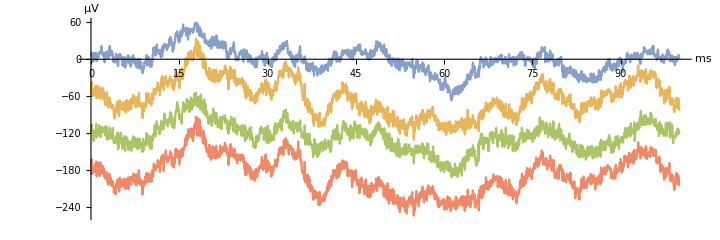

```mathematica
NNTracePlot[$nnwTestDataOri, All, {0 ;; 3200, 0}, NNOptAmplificationFactor-> 16]
```

```mathematica
NNTracePlotManipulate[$nnwTestDataOri, All, Automatic,
 NNOptAmplificationFactor-> 16]
```

!!!Always delete manipulate interface before proceeding!!!

```mathematica
$nnwTestDataMedianSubtract=NNFilterMedianSubtract[$nnwTestDataOri, 81]
```

## Old Initialization

```mathematica
resourceDataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]], "_resources","nounou","Neuralynx"}]
```

C:\prog\_w\NounouW\NounouW\Tests\_resources\nounou\Neuralynx

```mathematica
FileExistsQ[resourceDataDirectory]
```

True

## BG001 (short snippet)

```mathematica
tempDataFiles=FileNames["*.ncs",FileNameJoin[{resourceDataDirectory,"BG001","2016-05-11_16-34-20", "split","t0508_001", "segment 1","1-1"}]];
```

```mathematica
testBG001 = NNLoad[tempDataFiles]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
NNPrintInfo[ testBG001, "Timing" ]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	      2560 (  0:00.08) (     0.1)	  3401478496 ( 0:00.00)

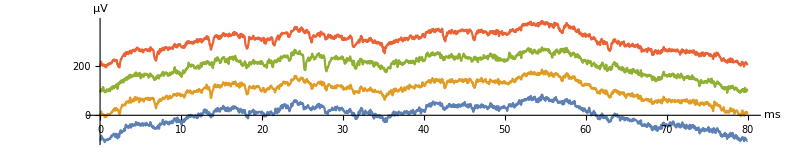

```mathematica
NNTracePlot[ testBG001, All, All, NNOptStack-> 100, AspectRatio-> 1/5, ImageSize-> 72*11]
```

## SPP010 (tetrode, one long segment)

```mathematica
testSPP010 = NNLoad[ FileNameJoin[{resourceDataDirectory,"SPP010","2013-12-02_17-07-31",#}]& /@{"Tet4a.ncs","Tet4b.ncs","Tet4c.ncs","Tet4d.ncs"} ]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
NNPrintInfo[ testSPP010, "Timing" ]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	 151597056 ( 78:57.41) (  4737.4)	 19228868023 ( 0:00.00)

HHStackLists::invalidOptionValue: Option argument HHOptStack -> None is invalid.

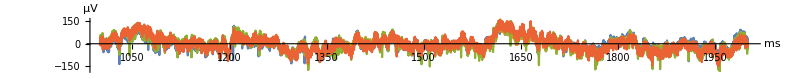

```mathematica
NNTracePlot[testSPP010, All, { 32001;;64000,0}, AspectRatio-> 1/10, ImageSize->11*72, NNOptStack-> None]
```

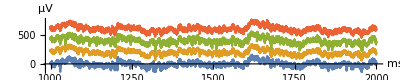

```mathematica
NNTracePlot[testSPP010, All, { 32001;;64000,0}, AspectRatio-> 1/5, ImageSize->Full, NNOptStack-> 200]
```

```mathematica
AbsoluteOptions[%, PlotRange]
```

{PlotRange→{{1000.03,2000.},{-141.291,761.266}}}

```mathematica
NNTracePlotManipulate[ testSPP010, All ]
```

## SPP010 (single channel, many segments)

### NNDataDownsample

```mathematica
testNCS1Downsample = NNDataDownsample[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Downsample ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Downsample,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### NNDataDecimate

```mathematica
testNCS1Decimate = NNDataDecimate[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Decimate ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Decimate,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-